```mathematica
ClearAll["Global`*"]
```

# Example Plotting Script for the Gershgorin-Harlim-Majda 2010 System

## Import Data

```mathematica
hereDir = NotebookDirectory[];
dataDir = FileNameJoin[{hereDir,"..","build"}];
runCount = 250;
importNetCDFArg = {"Datasets",Table[StringJoin["run",StringPadLeft[ToString[i],8,"0"]],{i,1,runCount}]};
rawData = Import[FileNameJoin[{dataDir,"out.nc"}],importNetCDFArg];
```

## Single-Run Plot

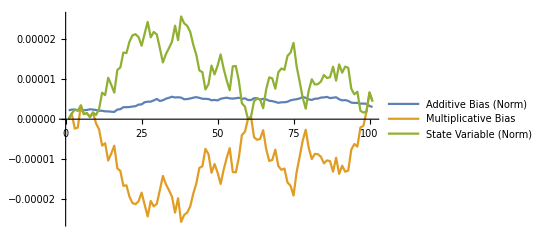

```mathematica
runNum = 2;
timeStepNum = rawData[[runNum]][[;;,1]];
time=rawData[[runNum]][[;;,2]];
addBias = rawData[[runNum]][[;;,3]] + ⅈ rawData[[runNum]][[;;,4]];
multBias = rawData[[runNum]][[;;,5]];
stateVar = rawData[[runNum]][[;;,6]] + ⅈ rawData[[runNum]][[;;,7]];

ListLinePlot[{Abs[addBias],multBias,Abs[multBias]},PlotRange->All,PlotLegends->{"Additive Bias (Norm)", "Multiplicative Bias", "State Variable (Norm)"}]
```

## Multi-Run Mean Plot

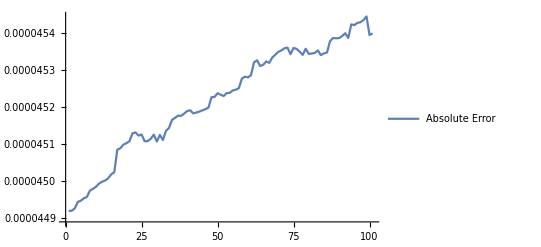

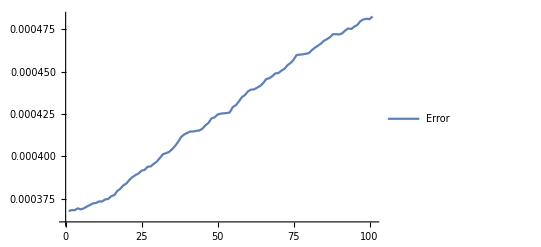

```mathematica
t0 = 0.0;
Δt = 0.00005;
meanB = 0.0+ⅈ 0.0;
meanB0 = 0.0 + ⅈ 0.0;
dampB = 0.15;
oscFreqB = 1.78;
lambdaB = -dampB + ⅈ oscFreqB;
meanBAnal[t_,t0_]:= meanB + (meanB0 - meanB)ⅇ^(lambdaB (t - t0))
meanGamma = 1.5;
meanGamma0 = 0.0;
dampGamma = 0.015;
meanGammaAnal[t_,t0_]:=meanGamma + (meanGamma0 - meanGamma)ⅇ^(-dampGamma(t - t0))
meanAddBias=Mean[rawData[[;;,;;,3]] + ⅈ rawData[[;;,;;,4]]];
meanMultBias = Mean[rawData[[;;,;;,5]]];
meanStateVar = Mean[rawData[[;;,;;,6]] + ⅈ rawData[[;;,;;,7]]];
ListLinePlot[{Table[Abs[meanBAnal[t0 + i * Δt,t0]-meanAddBias[[i+1]]],{i,0,Length[meanAddBias]-1}]},PlotLegends->{"Absolute Error"}]
ListLinePlot[{Table[meanGammaAnal[t0 + i * Δt,t0] - meanMultBias[[i+1]],{i,0,Length[meanMultBias]-1}]},PlotLegends->{"Error"}, PlotRange->All]
```